```mathematica
Plot[5,6]
```

Plot::pllim: Range specification 6 is not of the form {x, xmin, xmax}.

Plot[5,6]

```mathematica
PlotPoints[5,6]
```

PlotPoints[5,6]

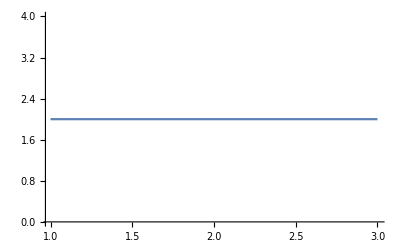

```mathematica
ListPlot[{{0.01,23},{0.02,10},{0.03,6},{0.04,4},{0.05,3},{0.06,2},{0.07,1},{0.08,1},{0.083,1}},Joined->True]
```

```mathematica
n=1/(4k)-2;
Plot[n,0,0.09]
```

Plot::nonopt: Options expected (instead of 0.09) beyond position 2 in Plot[n,0,0.09]. An option must be a rule or a list of rules.

Plot[n,0,0.09]

```mathematica
Plot[Floor[1/(4k)-2],{k,0,0.09},AxesLabel{"max possib","max possible n"}]
```

Plot::nonopt: Options expected (instead of AxesLabel {max possib,max possible n}) beyond position 2 in Plot[Floor[1/(4 k)-2],{k,0,0.09},AxesLabel {max possib,max possible n}]. An option must be a rule or a list of rules.

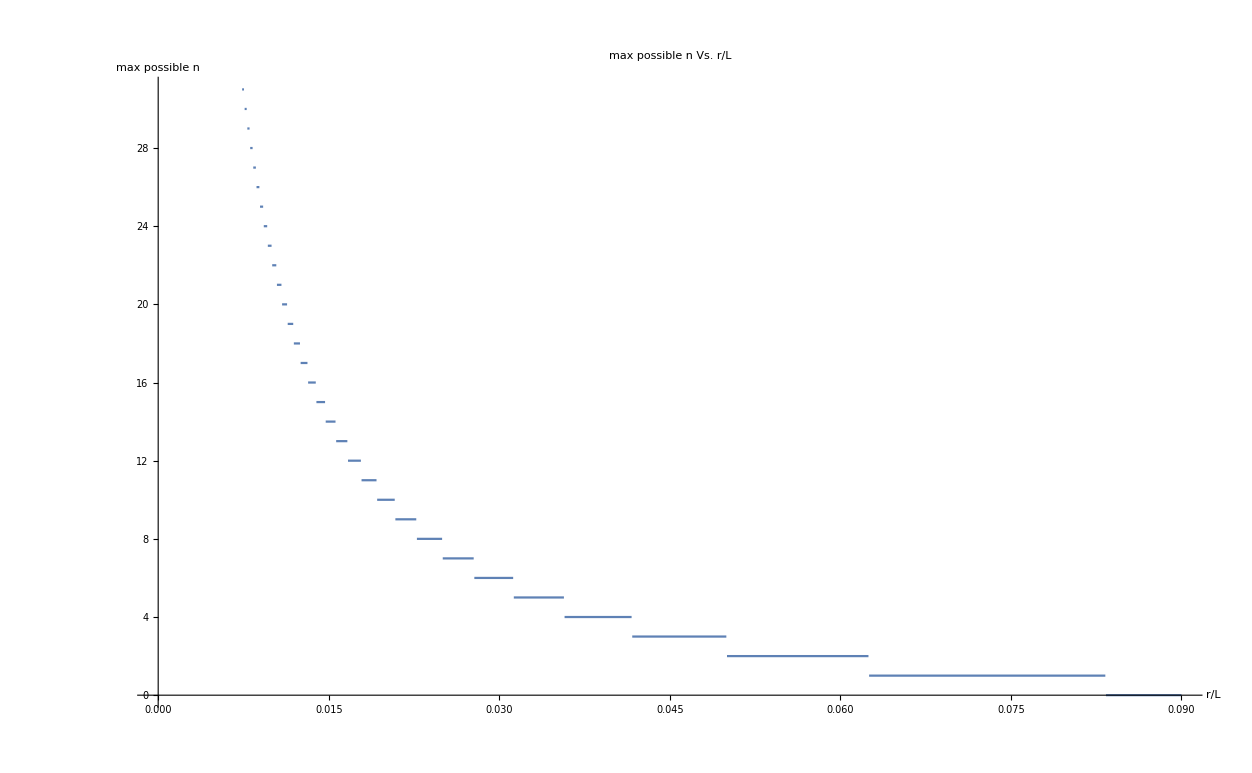

-Graphics-

```mathematica
Plot[Floor[1/(4 k)-2],{k,0,0.09},AxesLabel ->{"r/L","max possible n"},PlotLabel->"max possible n Vs. r/L"]
```